```mathematica
Zeta[s]/Zeta[1-s]/.{s->0.3}
```

0.32557

```mathematica
Gamma[0.3]
```

2.99157

```mathematica
Integrate[x^(s-1)ⅇ^-x/.{s->0.3},{x,0,∞}]
```

2.99157

```mathematica
Integrate[Abs[x]^(s-1)ⅇ^(2π ⅈ x)/.{s->0.3},{x,-∞,∞}]
```

3.07154+0. ⅈ

```mathematica
GZeta[x_]:=π^(-x/2)Gamma[x/2]
```

```mathematica
GZeta[s]/GZeta[1-s]/.{s->0.3}
```

3.07154

```mathematica
ZZeta[x_]:=π^(-x/2)Gamma[x/2]Zeta[x]
```

```mathematica
ZZeta[0.7]
```

-4.73886

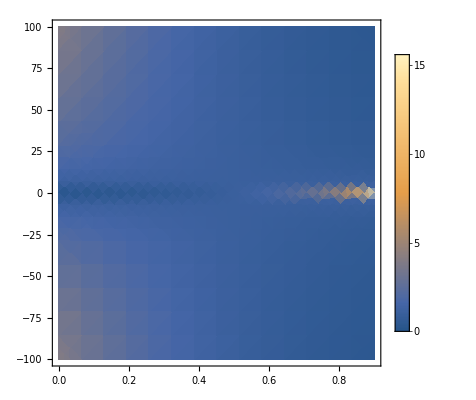

```mathematica
DensityPlot[Abs[Zeta[x+ⅈ y]/Zeta[1-(x+ⅈ y)]],{x,0,0.9},{y,-100,100},PlotLegends->Automatic,PlotRange->All]
```